# Nonlinear system solver by using a dynamical system

## [20150601] File created by Martín Villanueva [20150601] File modified in class, INF-482.

```mathematica
Solve[x^2+(y^2)/2==1 && x+y==1]
```

{{x→-1/3,y→4/3},{x→1,y→0}}

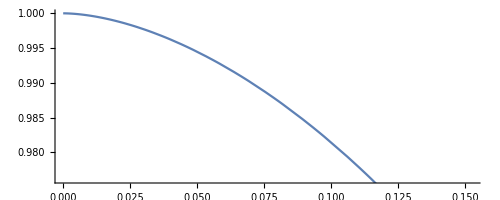

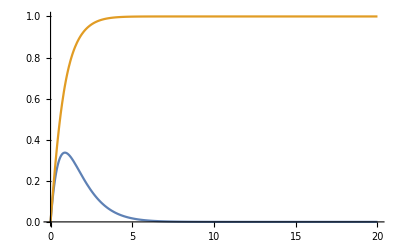

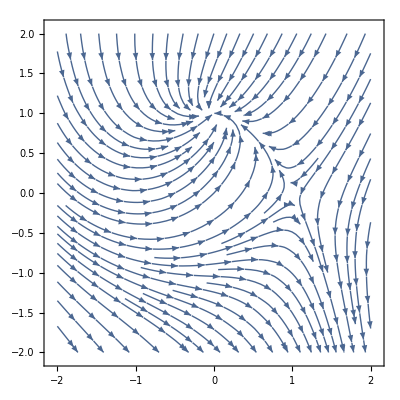

```mathematica
alpha=1;
beta=1;
s=NDSolve[{x'[t]==alpha*(1-x[t]-y[t]),y'[t]==beta(1-x[t]^2-y[t]^2),x[0]==0,y[0]==0},{x,y},{t,50}];
ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,20}]
Plot[Evaluate[{x[t],y[t]}/.s],{t,0,20}]
StreamPlot[{alpha(1-x-y),beta(1-x^2-y^2)},{x,-2,2},{y,-2,2}]
```

## Building the Jacobian matrix

```mathematica
m={{-α,-α},{-2β x,-2 y β }}
```

{{-α,-α},{-2 x β,-2 y β}}

```mathematica
EVs1=Eigenvalues[m]/.x->1 /.y->0
EVs2=FullSimplify[Eigenvalues[m]/.x->0 /.y->1]
```

{1/2 (-α-√(α^2+8 α β)),1/2 (-α+√(α^2+8 α β))}

{-α/2-1/2 √((α-2 β)^2)-β,1/2 (-α+√((α-2 β)^2)-2 β)}

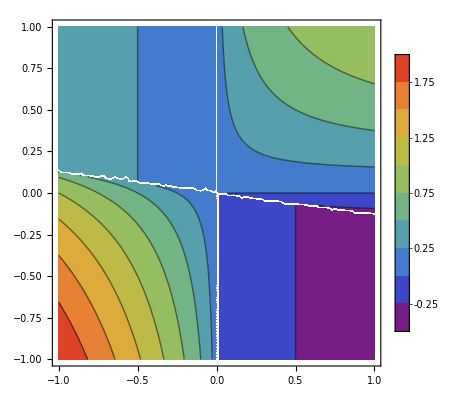

```mathematica
ContourPlot[Max[Re[EVs1]],{α,-1,1},{β,-1,1},ColorFunction->"Rainbow",PlotLegends->Automatic]
```

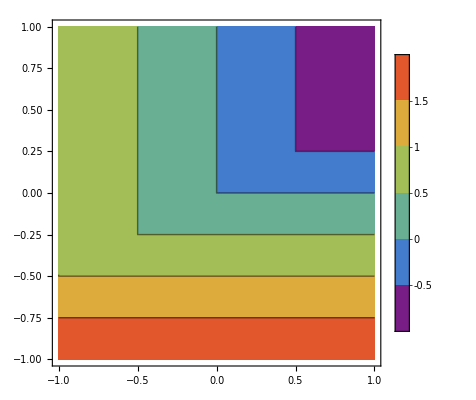

```mathematica
ContourPlot[Max[Re[EVs2]],{α,-1,1},{β,-1,1},ColorFunction->"Rainbow",PlotLegends->Automatic]
```

```mathematica
EVs1/.α->1/.β->-1
```

{1/2 (-1-ⅈ √7),1/2 (-1+ⅈ √7)}

```mathematica
EVs2/.α->1/.β->1
```

{-2,-1}